## Figure 1: Bifurcation plots for two species

```mathematica
Subscript[f, 1][x_]=Exp[-(Subscript[ϵ, 1]-x)^2/(2 Subscript[σ, 1]^2)];
Subscript[f, 2][x_]=Exp[-(Subscript[ϵ, 2]-x)^2/(2 Subscript[σ, 2]^2)];
```

```mathematica
f[x_]=Subscript[η, 1](Subscript[ϵ, 1]-x)Subscript[f, 1][x]+Subscript[η, 2](Subscript[ϵ, 2]-x)Subscript[f, 2][x];
```

```mathematica
par={Subscript[σ, 1]->1, Subscript[σ, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1,Subscript[ϵ, 1]->0};
```

#### · Find bifurcation point to robustly run FindRoot in domains that does not contain the bifurcation point.

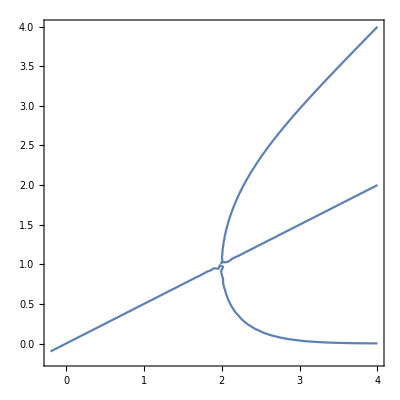

```mathematica
ContourPlot[(f[x]/.par)==0,{Subscript[ϵ, 2],-0.2,4},{x,-0.2,4}]
```

#### · Findroot initial condition need to be carefully chosen for the root finding method to converge (Choose based on the contour plot above). Set initial condition at (2,0.5) for η_1=1, and (2,2) for η_1=1.2.

```mathematica
bp=FindRoot[{f[x]/.par,D[f[x],x]/.par},{{Subscript[ϵ, 2],2},{x,0.5}}]
```

{ϵ_2→2.,x→0.999995}

#### Figure 1a

```mathematica
l1=Table[i,{i,0,Subscript[ϵ, 2]/.bp,0.01}];n1=Length[l1];
R1=Array[NaN,n1];
P1=Array[NaN,{n1,2}];
```

```mathematica
For[i=1,i≤n1,i++,{R1[[i]]=x/.FindRoot[f[x]/.{Subscript[ϵ, 2]->l1[[i]]}/.par,{x,0.5},MaxIterations->10000],P1[[i,1]]=Subscript[f, 1][x]/.par/.x->R1[[i]],P1[[i,2]]=Subscript[f, 2][x]/.par/.x->R1[[i]]/.Subscript[ϵ, 2]->l1[[i]]}];
```

```mathematica
fig1=ListPlot[TemporalData[R1,{l1}],Axes->False,Frame->True,FrameLabel->{"Soil preference ϵ_2","Equilibrium soil E^*"},LabelStyle->{FontSize->15,FontFamily->"Serif",Black},PlotRange->{{0,3.25},{0,3.25}},Joined->True,PlotStyle->{ColorData[97,1]}];
```

```mathematica
l2=Table[i,{i,0.01+Subscript[ϵ, 2]/.bp,3.25,0.01}];n2=Length[l2];
R2=Array[NaN,{n2,3}];
P2=Array[NaN,{n2,3,2}];
```

#### · Findroot initial condition need to be carefully chosen for the root finding method to converge (Choose (x/.bp). Set initial condition at (x/.bp)+0.2 for η_1=1, (x/.bp) for η_1=1.2, and .

```mathematica
For[i=1,i≤ n2,i++,{
R2[[i,1]]=x/.FindRoot[f[x]/.{Subscript[ϵ, 2]-> l2[[i]]}/.par,{x,0}],
R2[[i,2]]=x/.FindRoot[f[x]/.{Subscript[ϵ, 2]-> l2[[i]]}/.par,{x,(x/.bp)},MaxIterations->1000],
R2[[i,3]]=x/.FindRoot[f[x]/.{Subscript[ϵ, 2]-> l2[[i]]}/.par,{x,l2[[i]]}],For[j=1,j≤ 3,j++,{P2[[i,j,1]]=Subscript[f, 1][x]/.par/.x->R2[[i,j]],P2[[i,j,2]]=Subscript[f, 2][x]/.par/.x->R2[[i,j]]/.Subscript[ϵ, 2]->l2[[i]]}]}];
```

```mathematica
fig2=ListPlot[TemporalData[R2,{l2}],Axes->False,Frame->True,PlotRange->{{0,3.25},{0,3.25}},Joined->True,PlotStyle->{{ColorData[97,2]},{LightGray,Thickness[0.001]},{ColorData[97,3]}}];
```

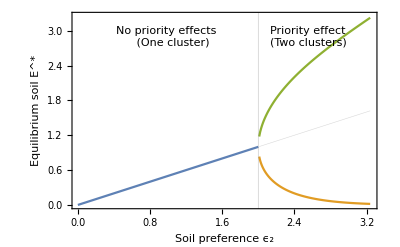

```mathematica
fig1a=Show[fig1,fig2,GridLines->{{{Subscript[ϵ, 2]/.bp,Thick}},{}},Epilog-> {Inset[Text[Style["No priority effects 
   (One cluster)",FontSize->13]],{1,2.9}],Inset[Text[Style["Priority effect
(Two clusters)",FontSize->13]],{2.55,2.9}]}]
```

#### Figure 1b

```mathematica
figP11=ListPlot[TemporalData[P1[[All,1]],{l1}],Axes->False,Frame->True,FrameLabel->{"Soil preference ϵ_2","Equilibrium abundance N_1^*"},LabelStyle->{FontSize->15,FontFamily->"Serif",Black},PlotRange->{{0,3.25},{0,1}},Joined->True,PlotStyle->ColorData[97,1]];
```

```mathematica
figP21=ListPlot[TemporalData[P2[[All,All,1]],{l2}],Axes->False,Frame->True,PlotRange->{{0,4},{0,1}},Joined->True,PlotStyle->{{ColorData[97,2]},{LightGray,Thickness[0.001]},{ColorData[97,3]}}];
```

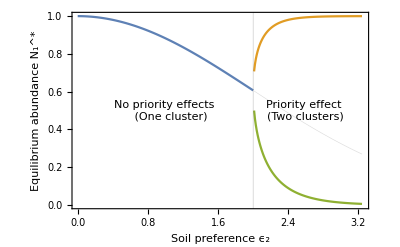

```mathematica
fig1b=Show[figP11,figP21,GridLines->{{{Subscript[ϵ, 2]/.bp,Thick}},{}},Epilog-> {Inset[Text[Style["No priority effects 
   (One cluster)",FontSize->13]],{1,0.5}],Inset[Text[Style["Priority effect 
(Two clusters)",FontSize->13]],{2.6,0.5}]}]
```

#### Figure 1c

```mathematica
Subscript[DN, 1]=Subscript[N, 1][t](1-(Subscript[N, 1][t])/Exp[-(r[t]-Subscript[ϵ, 1])^2/(2 Subscript[σ, 1]^2)]);
Subscript[DN, 2]=Subscript[N, 2][t](1-(Subscript[N, 2][t])/Exp[-(r[t]-Subscript[ϵ, 2])^2/(2 Subscript[σ, 2]^2)]);
Dr=Subscript[η, 1](Subscript[ϵ, 1]-r[t])Subscript[N, 1][t]+Subscript[η, 2](Subscript[ϵ, 2]-r[t])Subscript[N, 2][t];
```

```mathematica
par={Subscript[σ, 1]->1, Subscript[σ, 2]->1,Subscript[η, 1]->1,Subscript[η, 2]->1,Subscript[ϵ, 1]->0,Subscript[ϵ, 2]->2.5};
x0=1; y0=1; T=100;
Dxp=Subscript[DN, 1]/.par/.{Subscript[N, 1][t]->x[t],Subscript[N, 2][t]->y[t],r[t]->z[t]};
Dyp=Subscript[DN, 2]/.par/.{Subscript[N, 1][t]->x[t],Subscript[N, 2][t]->y[t],r[t]->z[t]};
Dzp=Dr/.par/.{Subscript[N, 1][t]->x[t],Subscript[N, 2][t]->y[t],r[t]->z[t]};
```

```mathematica
l3=Table[i,{i,Subscript[ϵ, 1]/.par,0.75+Subscript[ϵ, 2]/.par,0.02}];n3=Length[l3];
RA3=Array[NaN,n3];
```

```mathematica
For[i=1,i≤n3,i++,{nsol=NDSolve[{D[x[t],t]==Dxp,D[y[t],t]==Dyp,D[z[t],t]==Dzp,x[0]==x0,y[0]==y0,z[0]==l3[[i]]},{x,y,z},{t,0,T}],RA=(x[T]/(x[T]+y[T]))/.nsol,RA3[[i]]=RA[[1]]}];
```

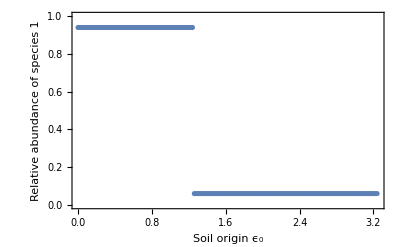

```mathematica
fig1c=ListPlot[TemporalData[RA3,{l3}],Axes->False,Frame->True,FrameLabel->{"Soil origin ϵ_0","Relative abundance of species 1"},LabelStyle->{FontSize->15,FontFamily->"Serif",Black},PlotRange->{{0,3.25},{0,1}},Joined->False,PlotStyle->{ColorData[97,1]}]
```